```mathematica
Subscript[BSpline, i_,0][x_,xList_]:=If[xList[[i]]≤x≤xList[[i+1]],1,0];
Subscript[BSpline, i_,k_][x_,xList_]:=Subscript[BSpline, i,k][x,xList]=(x-xList[[i]])/(xList[[i+k]]-xList[[i]])Subscript[BSpline, i,k-1][x,xList] + (xList[[i+k+1]]-x)/(xList[[i+k+1]]-xList[[i+1]])Subscript[BSpline, i+1,k-1][x,xList];
```

```mathematica
xList={0,.1,.2,.3,.4,.5,.6,.7,.8,.9,1,1.1,1.2,1.3,-.2,-.1};
```

```mathematica
Plot[Evaluate[Table[Subscript[BSpline, i,1][x,xList],{i,0,10}]],{x,0,1},PlotRange->All]
```

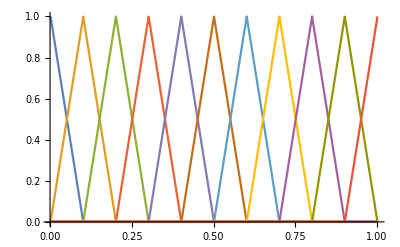

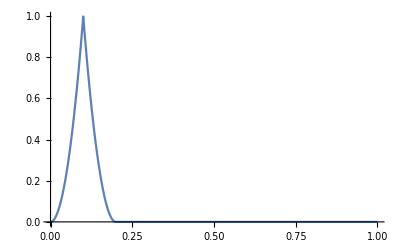

```mathematica
Plot[Subscript[BSpline, 1,1][x,xList]*Subscript[BSpline, 1,1][x,xList],{x,0,1},PlotRange->All]
```

```mathematica
Integrate[-n^2 t^2+(2i+1)n t - (i^2+i),{t,i/n,(i+1)/n}]
```

1/(6 n)